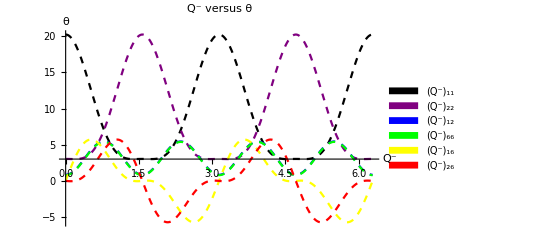

```mathematica
Subscript[U, 1]=9.34;
Subscript[U, 2]=8.60115;
Subscript[U, 3]=2.3;
Subscript[U, 4]=3.15;
Subscript[U, 5]=3.0967;
Legended [
Show[Plot[Subscript[U, 1]+Subscript[U, 2] Cos[2*θ]+Subscript[U, 3] Cos[4θ],{θ,0,2*π},PlotStyle -> {Black,Dashed}],
Plot[Subscript[U, 1]-Subscript[U, 2] Cos[2*θ]+Subscript[U, 3] Cos[4θ],{θ,0,2*π},PlotStyle -> {Purple,Dashed}],
Plot[Subscript[U, 4]-Subscript[U, 3] Cos[4*θ],{θ,0,2*π},PlotStyle -> {Blue,Dashed}],
Plot[Subscript[U, 5]-Subscript[U, 3] Cos[4*θ],{θ,0,2*π},PlotStyle -> {Green,Dashed}],
Plot[1/2*Subscript[U, 2] Sin[2*θ]+Subscript[U, 3] Sin[4θ],{θ,0,2*π},PlotStyle -> {Yellow,Dashed}],
Plot[1/2*Subscript[U, 2] Sin[2*θ]-Subscript[U, 3] Sin[4θ],{θ,0,2*π},PlotStyle -> {Red,Dashed}],
PlotLabel -> "Q^- versus θ",
AxesLabel -> {"Q^-","θ"},
PlotRange -> All],
SwatchLegend[{Black,Purple,Blue,Green,Yellow,Red},{"(Q^-)_11","(Q^-)_22","(Q^-)_12","(Q^-)_66","(Q^-)_16","(Q^-)_26"}]]
```